```mathematica
Qfield[x_]:=(({{0, -1}, {1, 0}}).x)/(2π Max[x.x,0.001])
```

```mathematica
Условия задачи
```

```mathematica
ν=(*1/1000*)10^-5;τ=0.01;eps=0.0001;Vinf={1,0};KMax=200;
```

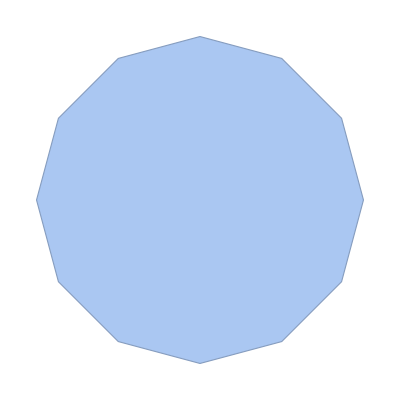

```mathematica
Rdots=Table[{Cos[t],Sin[t]},{t,0,2Pi-0.01,Pi/6}];
Rarea=BoundaryMeshRegion[Rdots,Line[Append[Range[1,Length@Rdots],1]]]
```

```mathematica
Rmids=(RotateLeft@Rdots+Rdots)/2;
Rsides=(RotateLeft@Rdots-Rdots);
rotRsides=RotateLeft@Rsides;
lSides=Table[√(Rsides[[i]].Rsides[[i]]),{i,Length@Rsides}];
```

```mathematica
Rnormals=Transpose@(({{0, -1}, {1, 0}}).Transpose@Rsides);
```

```mathematica
Rnormals=Table[Rnormals[[i]]/(√(Rnormals[[i]].Rnormals[[i]])),{i,Length@Rnormals}];
```

```mathematica
curlDeploy=1.05Rdots;
```

```mathematica
pics={};pics2={};
```

```mathematica
Предварительное составление матрицы и нахождение начальных вихрей
```

```mathematica
L1=Table[Qfield[Rmids[[i]]-curlDeploy[[j]]].Rnormals[[i]],{i,1,Length@Rdots},{j,1,Length@Rdots}];
newGamma=Table[{G[i]},{i,1,Length@Rdots}];
f0=Rnormals.Vinf;
curlsOnPanel={};
curlsInFlow={};
solution=Solve[{L1.newGamma+r==-f0,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]];
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution;
For[i=1,i≤Length@nGammaR-1,i++,AppendTo[curlsOnPanel,{nGammaR[[i]],curlDeploy[[i]]}]];
minCurl=Max[Abs@nGammaR]*0.001;
```

```mathematica
AllCurls=Join[curlsInFlow,curlsOnPanel];
Vfield=Vinf+Sum[First@AllCurls[[i]]Qfield[{x,y}-Last@AllCurls[[i]]],{i,Length@AllCurls}];
```

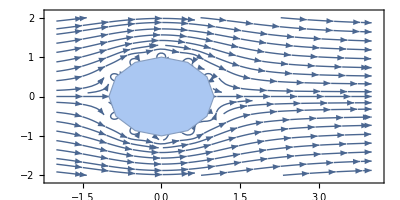

```mathematica
Show[StreamPlot[Vfield,{x,-2,4},{y,-2,2}],Rarea,AspectRatio->1/2]
```

```mathematica
ProgressIndicator[Dynamic[k/KMax]]
```

```mathematica
For[k=0,k<KMax,k++,
AllCurls=Join[curlsInFlow,curlsOnPanel];
f1=ParallelTable[Sum[Rnormals[[i]].Qfield[Rmids[[i]]-Last@AllCurls[[m]]]First@AllCurls[[m]],{m,1,Length@AllCurls}],{i,1,Length@curlDeploy}];
solution=Solve[{L1.newGamma+r==-f0-f1,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]];
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution;
For[i=1,i≤Length@curlsOnPanel,i++,
If[(Last@curlsOnPanel[[i]]-curlDeploy[[i]]).(Last@curlsOnPanel[[i]]-curlDeploy[[i]])<Min[lSides]^2/8,
curlsOnPanel[[i]][[1]]=curlsOnPanel[[i]][[1]]+nGammaR[[i]];
curlsOnPanel[[i]][[2]]=(Last@curlsOnPanel[[i]]*First@curlsOnPanel[[i]]+curlDeploy[[i]]*nGammaR[[i]])/(First@curlsOnPanel[[i]]+nGammaR[[i]]),
 AppendTo[curlsInFlow,curlsOnPanel[[i]]];(*слабое место, переделать!!!!*)
curlsOnPanel[[i]][[1]]=nGammaR[[i]];
curlsOnPanel[[i]][[2]]=curlDeploy[[i]];
]
(*If[(Last@curlsOnPanel[[i]]-curlDeploy[[i]]).(Last@curlsOnPanel[[i]]-curlDeploy[[i]])<Min[lSides]^2/4,
curlsOnPanel[[i]][[1]]=curlsOnPanel[[i]][[1]]+nGammaR[[i]]
]*)
];
AllCurls=Join[curlsInFlow,curlsOnPanel];

etaR=Table[{x,y}-Rmids[[i]],{i,Length@Rmids}]/eps;(*переделать в соответствии с диссером*)
modEtaR=Table[etaR[[i]].etaR[[i]],{i,Length@Rmids}];
primeR=Table[{x,y}-Last@(AllCurls[[i]]),{i,Length@AllCurls}];
modPrimeR=Table[primeR[[i]].primeR[[i]],{i,Length@AllCurls}];
I2=-Parallelize@Sum[primeR[[i]]/(√modPrimeR[[i]] eps) First@(AllCurls[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@AllCurls}];
I1=Parallelize@Sum[First@(AllCurls[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@AllCurls}];
I3=-Parallelize@Sum[Rnormals[[i]]Exp[-√modEtaR[[i]]],{i,Length@Rnormals}];
(*I3=-Parallelize@Sum[Rnormals[[i]]eps (1-Exp[-(√(Rsides[[i]].Rsides[[i]]))/(2 eps)]),{i,Length@Rnormals}];*)
I0=2π eps^2+Parallelize@Sum[(etaR[[i]].Rnormals[[i]])/modEtaR[[i]](√modEtaR[[i]]+1)Exp[-√modEtaR[[i]]]lSides[[i]],{i,Length@Rnormals}];
Wfield=ν(-I2/I1+I3/I0);
If[Length@curlsInFlow>0,
curlsInFlow=ParallelTable[{First@curlsInFlow[[i]],Last@(curlsInFlow[[i]])+τ (Vfield+Wfield)/.{x->First@Last@(curlsInFlow[[i]])(*+eps/1000*),y->Last@Last@(curlsInFlow[[i]])+eps/1000}},{i,Length@curlsInFlow}];]
curlsOnPanel=ParallelTable[{First@curlsOnPanel[[i]],Last@(curlsOnPanel[[i]])+τ (Vfield+Wfield)/.{x->First@Last@(curlsOnPanel[[i]])(*+eps/1000*),y->Last@Last@(curlsOnPanel[[i]])+eps/1000}},{i,Length@curlsOnPanel}];

(*Ufield[x0_]:=(Vfield+Wfield)/.{x->First@x0,y->Last@x0}*)
(*
curlsOnPanel={};
curlsInFlow={};*)
(*Определяем кандидатов под аннигиляцию и, пока есть такая возможность, без угрызений совести выпиливаем из списка*)
(*curlsToRemove={};*)
For[i=1,i≤Length@curlsOnPanel,i++,If[RegionMember[Rarea,Last@(curlsOnPanel[[i]])] ||Abs@ First@(curlsOnPanel[[i]])<minCurl,curlsOnPanel[[i]][[2]]=curlDeploy[[i]];curlsOnPanel[[i]][[1]]=nGammaR[[i]];];];
(*curlsOnPanel=Delete[curlsOnPanel,curlsToRemove];*)
curlsToRemove={};
For[i=1,i≤Length@curlsInFlow,i++,If[RegionMember[Rarea,Last@(curlsInFlow[[i]])] ||Abs@ First@(curlsInFlow[[i]])<minCurl,AppendTo[curlsToRemove,{i}]];];
curlsInFlow=Delete[curlsInFlow,curlsToRemove];
AllCurls=Join[curlsInFlow,curlsOnPanel];

Vfield=Vinf+Sum[First@AllCurls[[i]]Qfield[{x,y}-Last@AllCurls[[i]]],{i,Length@AllCurls}];
(*If[Mod[k,5]==0,
AppendTo[pics2,Show[(*ContourPlot[Vfield.Vfield,{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],*)StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]];
CurlsGraph=Table[Graphics[{White,Disk[Last@AllCurls[[i]],1/20]}],{i,Length@AllCurls}];
AppendTo[pics,Show[ContourPlot[0,{x,-2,4},{y,-2,2}],Rarea,CurlsGraph,AspectRatio->1/2]];]*)
]
```

Min::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √(1/4+(-1+(√3)/2)^2)-√((1/2-1/2 Power[«2»])^2+(-1/2+1/2 Power[«2»])^2).

Min::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √(1/4+(1-(√3)/2)^2)-√((1/2-1/2 Power[«2»])^2+(-1/2+1/2 Power[«2»])^2).

Min::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √2 (-1/2+(√3)/2)-√((1/2-1/2 Power[«2»])^2+(-1/2+1/2 Power[«2»])^2).

General::stop: Further output of Min::meprec will be suppressed during this calculation.

```mathematica
curlsInFlow
curlsOnPanel
```

{{0.467615,{5.70666,1.46284}},{0.339098,{9.35727,7.78912}},{-1.4494,{1.45053,0.430021}},{-1.58912,{1.16289,0.97444}},{0.091763,{1.0707,-0.20926}},{1.02203,{5.6742,-7.43905}},{0.166406,{0.759105,1.29192}},{-0.0624174,{1.118,0.0979916}},{0.152398,{1.1052,0.561949}},{-0.827228,{1.87507,0.193688}},{0.159037,{2.23336,-0.660807}},{-0.775281,{0.381159,1.16922}},{0.159841,{1.17215,-0.0912134}},{-0.33612,{0.575647,1.21996}},{0.494569,{0.432545,-1.05546}},{0.962673,{0.862117,-0.863742}},{-0.103607,{1.36277,-0.130103}},{-1.02204,{0.712068,4.69587}},{-1.27056,{0.039865,1.20134}},{-0.176026,{-0.659626,-1.25564}},{0.039306,{0.817438,0.772488}},{0.0270234,{-3.30496,5.73586}},{-0.0239822,{0.867463,-0.736214}},{-0.875922,{1.08723,1.31998}},{0.695625,{1.91727,0.178102}},{-0.0779661,{1.03749,0.42186}},{0.037145,{-0.0349848,1.27149}},{0.0224686,{0.46435,1.47685}},{0.152487,{0.995262,0.81754}},{-0.654148,{-0.423456,1.02768}},{0.0843366,{0.493875,1.0753}},{-0.0190917,{0.814585,-0.685352}},{-0.169355,{1.1646,1.63305}},{0.0698247,{0.385229,-0.964901}},{-0.00817289,{1.57784,-0.158693}},{0.509884,{0.069564,1.07229}},{0.00718231,{0.061844,1.35882}},{0.170013,{0.505842,1.21052}},{-0.820612,{-0.786488,0.834436}},{-0.102916,{0.818941,1.23617}},{-0.39312,{0.967635,-0.884071}},{0.166052,{-1.19911,-0.359067}},{0.85487,{-0.301306,-1.08215}},{-0.0557032,{-0.475174,1.13175}},{-0.00877151,{0.764828,-0.703481}}}

{{0.208154,{1.01697,0.0962382}},{0.405467,{0.917132,0.587497}},{0.0686388,{0.532338,0.915064}},{-0.363011,{0.01462,1.02664}},{0.0485553,{-0.521991,0.918925}},{-0.453257,{-0.927679,0.591601}},{-0.20614,{-1.01636,0.068658}},{0.173308,{-0.868548,-0.51968}},{0.268035,{-0.513724,-0.946605}},{0.4217,{0.0929197,-0.991611}},{-0.00411977,{0.526251,-0.905327}},{0.177702,{0.943812,-0.4085}}}

```mathematica
Length@curlsOnPanel
```

12

```mathematica
Length@pics
```

40

```mathematica
Export["tester2.gif",pics2]
```

tester2.gif

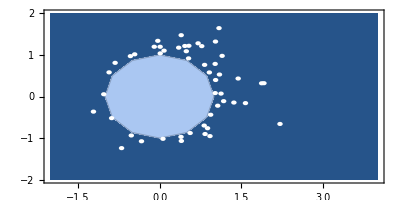

```mathematica
Last@pics
```

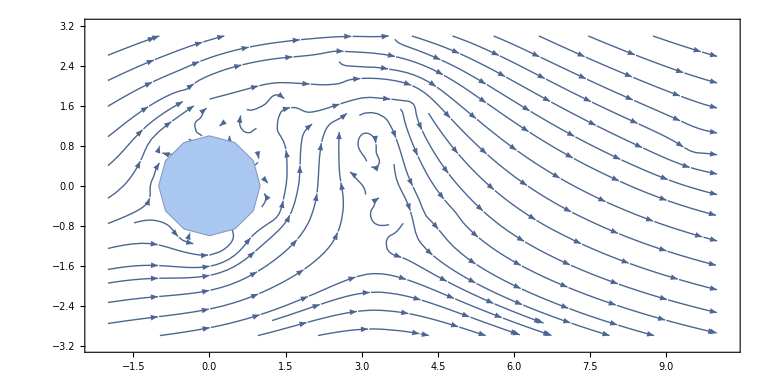

```mathematica
Show[(*ContourPlot[√(Vfield.Vfield),{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],*)StreamPlot[Vfield,{x,-2,10},{y,-3,3}(*,Mesh->5*)],Rarea,AspectRatio->1/2]
```